```mathematica
SetDirectory[NotebookDirectory[]];
matr=Delete[ReadList["./data/kvaziImplicit.txt", Real], 1];
xArr =Range[1, Length[matr]]/ Length[matr];
```

```mathematica
data=Thread[{xArr, matr}];
```

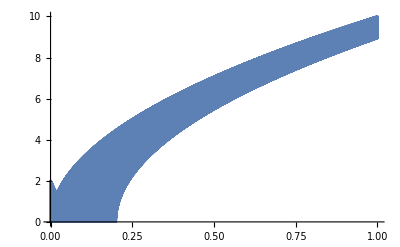

```mathematica
ListLinePlot[data]
```

```mathematica
(*Animate[ListLinePlot[matr[[i]]],{i,1,Length[matr],1}];*)
```